# Practical 3

## Third Order Ordinary Differential Equations

### Third order ordinary differential equations: The differential equations that involves the third order derivatives of dependent variable with respect to independent variable Command: DSolve[Differential Equation, y[x], x]

### Q1 Solve the following third order ordinary differential equation (d^3 y)/dx^3-27y = 0, c_1 = 1, c_2= -4, c_3 = 5

```mathematica
eqn= y'''[x] - 27y[x] == 0
```

-27 y[x]+y^(3)[x]==0

```mathematica
init = {C[1]-> 1, C[2] -> -4, C[3]->5 }
```

{C[1]→1,C[2]→-4,C[3]→5}

```mathematica
sol=y[x]/.DSolve[eqn, y[x], x][[1]]/.init
```

ⅇ^(3 x)-4 ⅇ^(-3 x/2) Cos[(3 √3 x)/2]+5 ⅇ^(-3 x/2) Sin[(3 √3 x)/2]

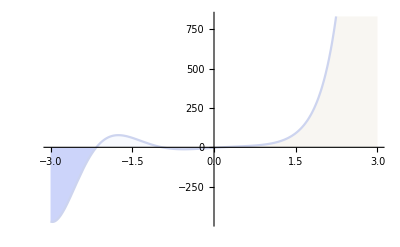

```mathematica
Plot[sol, {x, -3, 3}, ColorFunction->"TemperatureMap", PlotLegends->sol, Filling->Axis, FillingStyle->Opacity[0.3]]
```

### Q2 Solve the following third order ordinary differential equation (d^3 y)/dx^3-6(d^2 y)/dx^2 + 11 dy/dx-6y= 0, y(0) = 1, y'(0)= 5, y''(0) = 10

```mathematica
eqn= {y'''[x] - 6y''[x] + 11y'[x] - 6y[x] == 0, y[0] == 1, y'[0] == 5, y''[0] == 10}
```

{-6 y[x]+11 y'[x]-6 y''[x]+y^(3)[x]==0,y[0]==1,y'[0]==5,y''[0]==10}

```mathematica
sol=y[x]/.DSolve[eqn, y[x], x][[1]]
```

-1/2 ⅇ^x (9-14 ⅇ^x+3 ⅇ^(2 x))

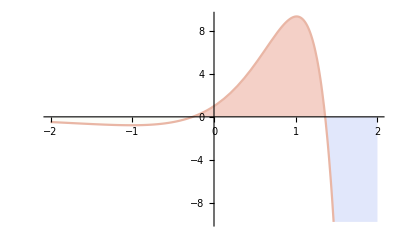

```mathematica
Plot[sol, {x, -2, 2}, ColorFunction->"TemperatureMap", PlotLegends->sol, Filling->Axis, FillingStyle->Opacity[0.3]]
```

### Q3 Solve the following third order ordinary differential equation (d^3 y)/dx^3-dy/dx= e^x

```mathematica
eqn= {y'''[x] - y'[x] == Exp[x]}
```

{-y'[x]+y^(3)[x]==ⅇ^x}

```mathematica
sol=y[x]/.DSolve[eqn, y[x], x][[1]]
```

ⅇ^x (x/2+1/4 (-3+4 C[1]))-ⅇ^-x C[2]+C[3]

### Q4 Solve the following third order ordinary differential equation (d^3 y)/dx^3+ dy/dx= 2 - sin(x), c_1 = 5, c_2= -2, c_3= 6

```mathematica
eqn= {y'''[x]+ y'[x]== 2 - Sin[x]}
```

{y'[x]+y^(3)[x]==2-Sin[x]}

```mathematica
init = {C[1]->5, C[2]->-2, C[3]->6}
```

{C[1]→5,C[2]→-2,C[3]→6}

```mathematica
sol=y[x]/.DSolve[eqn, y[x], x][[1]]/.init
```

6+2 x+(5 Cos[x])/2+5 Sin[x]+1/2 x Sin[x]

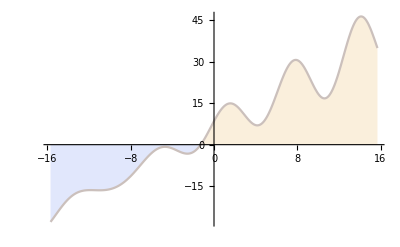

```mathematica
Plot[sol, {x, -5Pi, 5Pi}, ColorFunction->"TemperatureMap", PlotLegends->sol, Filling->Axis, FillingStyle->Opacity[0.3]]
```

### Q5 Solve the following third order ordinary differential equation (d^3 y)/dx^3- (d^2 y)/dx^2- 12 dy/dx= x -2x e^(-3x), c_1 = 12, c_2= 5, c_3= 1

```mathematica
eqn= {y'''[x]- y''[x]- 12y'[x]== x - 2x*Exp[-3x]}
```

{-12 y'[x]-y''[x]+y^(3)[x]==x-2 ⅇ^(-3 x) x}

```mathematica
init = {C[1]->12, C[2]->5, C[3]->1}
```

{C[1]→12,C[2]→5,C[3]→1}

```mathematica
sol=Simplify[y[x]/.DSolve[eqn, y[x], x][[1]]/.init]
```

(5 ⅇ^(4 x))/4+1/144 (144+x-6 x^2)-(ⅇ^(-3 x) (37202+420 x+441 x^2))/9261

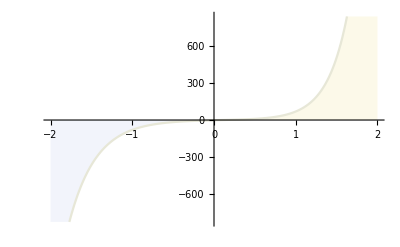

```mathematica
Plot[sol, {x, -2, 2}, ColorFunction->"TemperatureMap", PlotLegends->sol, Filling->Axis, FillingStyle->Opacity[0.3]]
```